# A mathematical model for universal semantics (Text mining in Turkish)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Turkish translation of Jane Austen’s Pride and Prejudice is commercially available from 
https://play.google.com/store/books/details/Jane_Austen_Gurur_ve_%C3%96nyarg%C4%B1?id=EfCEDwAAQBAJ

After manual cleansing, we save the text as Pride and Prejudice (Turkish).txt,  which begins with

BÖLÜM 1Hâli vakti yerinde bekâr bir erkeğin tek eksiğinin bir eş olduğu, herkesçe bilinen bir gerçektir.

Bir muhite ilk geldiğinde böyle bir erkeğin hisleri veya görüşleri hakkında pek bir şey bilinm

and ends with

samimi şekildeydi. Darcy de en az Elizabeth kadar onları seviyordu; ikisi de Elizabeth’i Derbyshire’a getirmek suretiyle birleşmelerine vesile olan bu kişilere karşı her daim büyük minnet beslediler.

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Turkish

## Turkish stop words

```mathematica
TurkishPronouns={"ben","biz","sen","siz","on","onlar","benim","bizim", "senin","sizin","onun","onların","bana","bize","sana","size","ona","onlara","beni","bizi","seni","sizi","onu","onları","benden","bizden","senden","sizden","ondan","onlardan","bende","bizde","sende","sizde","onda","onlarda"}∪{"bu","şu","bunlar","şunlar","bunun","şunun","bunların","şunların","buna","şuna","bunlara","şunlara","bunu","şunu","bunları","şunları","bundan","şundan","bunlardan","şunlardan","bunda","şunda","bunlarda","şunlarda"}∪{"kim","ne","nere","hangisi","kimler","neler","nereler","hangileri","kimin","neyin","nereyin","hangisinin","kimlerin","nerelerin","nelerin","hangilerinin","kime","neye","nereye","hangisine","kimlere","nelere","nerelere","hangilerine","kimi","nereyi","neyi","hangisini","kimleri","neleri","nereleri","hangilerini","kimden","neden","nereden","hangisinden","kimlerden","nelerden","nerelerden","hangsilerinden","kimde","nede","nerede","hangisinde","kimlerde","nerelerde","nelerde","hangsilerinde","hangi","hani"}∪{"bura","şura","ora","buralar","şuralar","oralar","burayı", "şurayı","orayı","buraları","şuraları","oraları","buradan","şuradan","oradan","buralardan","şuralardan","oralardan","burada","şurada","orada","buralarda","şuralarda","oralarda","buraya", "şuraya","oraya","buralara","şuralara","oralara","buranın","şuranın","oranın","buraların","şuraların","oraların"}∪{"hepsi","hepsini","hepsinden","hepsinde","hepsine","hepsinin"}∪{"bazıları","bazılarını","bazılarından","bazılarıda","bazılarına","bazılarının"};
```

```mathematica
TurkishStopWords=Complement[ToLowerCase[{"aşağı","aşağıda","aksi","altında","ama","ancak","andan","aralarında","arasında","aynı","ayrı","ayrıca","az","başına","başka","bazen","bazı","belgeyle","belki","bir","biraz","biri","birileri","birisi","birkaç","birlikte","bize","bizim","bizler","böyle","boylece","böylece","bu","buna","bundan","bunlar","bunun","bununla","burada","buradaki","buralarda","buraya","bütün","civarda","çok","çoğu","çoğunlukla","çünkü","da","daha","dahası","de","dışarı","diğer","diğerleri","dışında","dolayısıyla","edildi","eğer","şekilde","en","etrafında","etsen","ettik","evet","şey","fakat","gelen","gelişme","gereçler","gerektiği","geride","gibi","günü","hadi","hala","halde","haline","hangisi","hariç","hatta","hayır","hem","her","herhangi","herkes","herkesin","hiç","hiçbir","icar","içeride","için","içinde","içinden","içine","ile","ilgili","şimdi","şimdiye","irade","ister","işte","iyi","izin","kadar","kapalı","karşı","karşısında","kazanılmış","kenara","kez","ki","kişinin","kişiye","kim","kime","kimi","kimin","kimse","konum","mi","nasıl","ne","neden","nedenle","nerede","neredeyse","niçin","o","olacak","olan","olanları","oldu","oldukça","Olduğu","olma","olmadan","olmadı","olmadıkça","olmak","olmali","olmamalı","olmamalıdır","olmanın","olmaz","olmuştur","olsa","olsun","olup","olur","olurken","olursa","ön","önce","önde","onlar","onları","onların","onu","onun","orada","oralarda","ordan","ortasında","ötesinde","oysa","pek","sadece","sahip","sahiptir","sana","sayede","sen","senin","sırasında","sırt","son","sonra","sonradan","sonraki","tam","tarafından","tek","üstelik","uzak","üzerinde","üzerine","vakte","var","vardı","ve","verdim","vesile","vs","ya","yakında","yaklaşık","yani","yanında","yapamadım","yapamaz","yapar","yapıyor","yapma","yerine","yeterince","yine","yoluyla","yukarı","yukarıdaki","yüzden","zaman","zamanda","zaten"}∪{"mı","mu","mü"}∪{"yapacağım","yapacağız","yapacak","yapacaklar","yapacaksın","yapacaksınız","yapar","yaparım","yaparız","yaparlar","yaparsın","yaparsınız","yapıyor","yapıyordu","yapıyorduk","yapıyordum","yapıyordun","yapıyordunuz","yapıyorlar","yapıyorlardı","yapıyorsun","yapıyorsunuz","yapıyorum","yapıyoruz","yapmadı","yapmadık","yapmadılar","yapmadım","yapmadın","yapmadınız","yapmam","yapmayacağım","yapmayacağız","yapmayacak","yapmayacaklar","yapmayacaksın","yapmayacaksınız","yapmayız","yapmaz","yapmazlar","yapmazsın","yapmazsınız","yapmıyor","yapmıyordu","yapmıyorduk","yapmıyordular","yapmıyordum","yapmıyordun","yapmıyordunuz","yapmıyorlar","yapmıyorsun","yapmıyorsunuz","yapmıyorum","yapmıyoruz","yaptı","yaptık","yaptılar","yaptım","yaptın","yaptınız"}∪{"eder","ederim","ederiz","ederler","edersin","edersiniz","ediyor","ediyordu","ediyorduk","ediyordum","ediyordun","ediyordunuz","ediyorlar","ediyorlardı","ediyorsun","ediyorsunuz","ediyorum","ediyoruz"}∪{"eder","ederim","ederiz","ederler","edersin","edersiniz","ediyor","ediyordu","ediyorduk","ediyordum","ediyordun","ediyordunuz","ediyorlar","ediyorlardı","ediyorsun","ediyorsunuz","ediyorum","ediyoruz","etmedi","etmedik","etmediler","etmedim","etmedin","etmediniz","etmem","etmeyiz","etmez","etmezler","etmezsin","etmezsiniz","etmiyor","etmiyordu","etmiyorduk","etmiyordum","etmiyordun","etmiyordunuz","etmiyorlar","etmiyorlardı","etmiyorsun","etmiyorsunuz","etmiyorum","etmiyoruz","etti","ettik","ettiler","ettim","ettin","ettiniz"}∪TurkishPronouns∪{"daha","en"}∪{"olacağım","olacağız","olacak","olacaklar","olacaksın","olacaksınız","oldu","olduk","oldular","oldum","oldun","oldunuz","olmadı","olmadık","olmadılar","olmadım","olmadın","olmadınız","olmam","olmayacağım","olmayacağız","olmayacak","olmayacaklar","olmayacaksın","olmayacaksınız","olmayız","olmaz","olmazlar","olmazsın","olmazsınız","olmuyor","olmuyordu","olmuyorduk","olmuyordular","olmuyordum","olmuyordun","olmuyordunuz","olmuyorlar","olmuyorsun","olmuyorsunuz","olmuyorum","olmuyoruz","olur","olurlar","olursun","olursunuz","olurum","oluruz","oluyor","oluyordu","oluyorduk","oluyordum","oluyordun","oluyordunuz","oluyorlar","oluyorlardı","oluyorsun","oluyorsunuz","oluyorum","oluyoruz"}∪{"mı","mısın","mısınız","mıydı","mıyım","mıyız","mu","musun","musunuz","muydu","muyduk","muydum","muydun","muydunuz","muyum","muyuz"}∪{"mi","mı","misin","misiniz","mıydı","miyim","miyiz","mu","musun","musunuz","muydu","muyduk","muydum","muydun","muydunuz","muyum","muyuz"}∪{"ettirdi","ettirdik","ettirdiler","ettirdim","ettirdin","ettirdiniz","ettireceğim","ettireceğiz","ettirecek","ettirecekler","ettireceksin","ettireceksiniz","ettirir","ettiririm","ettiririz","ettirirler","ettirirsin","ettirirsiniz","ettiriyor","ettiriyordu","ettiriyorduk","ettiriyordum","ettiriyordun","ettiriyordunuz","ettiriyorlar","ettiriyorlardı","ettiriyorsun","ettiriyorsunuz","ettiriyorum","ettiriyoruz","ettirmedi","ettirmedik","ettirmediler","ettirmedim","ettirmedin","ettirmediniz","ettirmem","ettirmeyeceğim","ettirmeyeceğiz","ettirmeyecek","ettirmeyecekler","ettirmeyeceksin","ettirmeyeceksiniz","ettirmeyiz","ettirmez","ettirmezler","ettirmezsin","ettirmezsiniz","ettirmiyor","ettirmiyordu","ettirmiyorduk","ettirmiyordular","ettirmiyordum","ettirmiyordun","ettirmiyordunuz","ettirmiyorlar","ettirmiyorsun","ettirmiyorsunuz","ettirmiyorum","ettirmiyoruz"}∪{"ve","ile","da","de","hem","ne","gerek","ister","olsun","bir","kâh","kimi","kimisi","veya","ya","yahut","veyahut","ayrıca","üstelik","dahası","bile","hatta","ama","fakat","lâkin","ancak","oysa","halbuki","meğer","meğerse","çünkü","zira","dendenle","bu","sebeple","yüzden","dolayı","madem","mademki","eğer","şayet","keşke","örneğin","meselâ","sözgelimi","yani","yoksa","aksi","durumda","takdirde","meğerki"}∪{"için","gibi","kadar","göre","önce","evvel","sonra","ötürü","rağmen","karşın","üzere","karşı","başka"}∪{"ol","olarak","diye","anca","artık","a","e","eden","hemen","ise","ayrıca","ayriyeten","ayrıyeten","salt","neyse","tabii","beri","henüz","hâlâ","dek","tekrar","ki","gayet","sık","hakkında","dair"}],{"not","could","a","hereunto","thine","on","er"}];
```

```mathematica
DictionaryLookup[Alternatives@@TurkishStopWords]
```

{bile,biz,en,hem,her,mi,mu,salt,size,son,tam,vs,ya}

```mathematica
TurkishReflexivePronouns="kendi"~~"m"|"n"|"si"|"miz"|"niz"|"leri"~~""|"n"~~""|"i"|"den"|"de"|"e"|"in";
```

```mathematica
TurkishPossessivePronouns="benim"|"senin"|"onun"|"bizim"|"sizin"|"onların"~~""|"ki"|"kin"~~""|"i"|"den"|"de"|"e"|"in";
```

### Sample words

```mathematica
readTurkish={"okudu","okuduk","okudular","okudum","okudun","okudunuz","okumadı","okumadık","okumadılar","okumadım","okumadın","okumadınız","okumam","okumayacağım","okumayacağız","okumayacak","okumayacaklar","okumayacaksın","okumayacaksınız","okumayız","okumaz","okumazlar","okumazsın","okumazsınız","okumuyor","okumuyordu","okumuyorduk","okumuyordular","okumuyordum","okumuyordun","okumuyordunuz","okumuyorlar","okumuyorsun","okumuyorsunuz","okumuyorum","okumuyoruz","okur","okurlar","okursun","okursunuz","okurum","okuruz","okuyacağım","okuyacağız","okuyacak","okuyacaklar","okuyacaksın","okuyacaksınız","okuyor","okuyordu","okuyorduk","okuyordum","okuyordun","okuyordunuz","okuyorlar","okuyorlardı","okuyorsun","okuyorsunuz","okuyorum","okuyoruz"};
```

```mathematica
buyTurkish={"al","alacağım","alacağız","alacak","alacaklar","alacaksın","alacaksınız","aldı","aldık","aldılar","aldım","aldın","aldınız","alır","alırım","alırız","alırlar","alırsın","alırsınız","alıyor","alıyordu","alıyorduk","alıyordum","alıyordun","alıyordunuz","alıyorlar","alıyorlardı","alıyorsun","alıyorsunuz","alıyorum","alıyoruz","almadı","almadık","almadılar","almadım","almadın","almadınız","almam","almayacağım","almayacağız","almayacak","almayacaklar","almayacaksın","almayacaksınız","almayız","almaz","almazlar","almazsın","almazsınız","almıyor","almıyordu","almıyorduk","almıyordular","almıyordum","almıyordun","almıyordunuz","almıyorlar","almıyorsun","almıyorsunuz","almıyorum","almıyoruz"};
```

```mathematica
sayTurkish={"dedi","dedik","dediler","dedim","dedin","dediniz","demedi","demedik","demediler","demedim","demedin","demediniz","demem","demeyeceğim","demeyeceğiz","demeyecek","demeyecekler","demeyeceksin","demeyeceksiniz","demeyiz","demez","demezler","demezsin","demezsiniz","demiyor","demiyordu","demiyorduk","demiyordular","demiyordum","demiyordun","demiyordunuz","demiyorlar","demiyorsun","demiyorsunuz","demiyorum","demiyoruz","der","derim","deriz","derler","dersin","dersiniz","dimeyecek","dimeyecekler","diyeceğim","diyeceğiz","diyecek","diyecekler","diyeceksin","diyeceksiniz","diyor","diyordu","diyorduk","diyordum","diyordun","diyordunuz","diyorlar","diyorlardı","diyorsun","diyorsunuz","diyorum","diyoruz"};
```

```mathematica
houseTurkish={"ev","evde","evden","eve","evi","evin","evler","evlerde","evlerden","evlere","evleri","evlerin"};
```

```mathematica
bookTurkish={"kitaba","kitabı","kitabın","kitap","kitaplar","kitaplara","kitaplarda","kitaplardan","kitapları","kitapların","kitapta","kitaptan"};
```

## Approximate clustering of Turkish words

The clustering routine is described below.

### Effective spelling and essential root

```mathematica
TurkishEffVowels="a"|"â"|"e"|"ı"|"i"|"î"|"o"|"ö"|"u"|"û"|"ü";
```

```mathematica
TurkishProtectedRange[s_]:=If[StringContainsQ[s,TurkishEffVowels],First[First[StringPosition[s,TurkishEffVowels]]],0]
```

```mathematica
RegTurkishAdj[s_]:=(prep=StringReplace[StringReplace[s,{WordBoundary~~(h:((cv1:(Except[TurkishEffVowels]~~TurkishEffVowels))~~"m"|"p"|"r"|"s"~~(cv2:(Except[TurkishEffVowels]~~TurkishEffVowels)))):>If[cv1==cv2,cv2,h]}],{WordBoundary~~"apacı":>"acı",WordBoundary~~"uzun"~~___:>"λoνγ",WordBoundary~~"ıpıslak":>"ıslak",WordBoundary~~"ad":>"naμ",WordBoundary~~"mrs"~~WordBoundary:>"φραu",WordBoundary~~"mr"~~WordBoundary:>"ηeρρ",WordBoundary~~"emin"~~___:>"σuρϵ",WordBoundary~~"emel":>"eμeλ"}];StringTake[prep,TurkishProtectedRange[prep]]<>(prep1=StringReplace[StringDrop[prep,TurkishProtectedRange[prep]],{""|"y"~~"ı"|"i"|"u"|"ü"~~"p"~~WordBoundary:>"","c"|"ç"~~"a"|"e"~~WordBoundary:>"","c"|"ç"~~"ı"|"i"~~"k"~~WordBoundary:>"",""|"u"~~"ms"~~"ı"|"i"|"u"~~WordBoundary:>"",""|"u"~~"mt"~~"ı"|"i"~~"rak"~~WordBoundary:>""}];If[StringContainsQ[prep1,(("s"~~"ı"|"i"|"u"|"ü"))~~"z"],"ν"<>StringReplace[prep1,(("s"~~"ı"|"i"|"u"|"ü"))~~"z"~~___:>""],prep1]))
```

```mathematica
TurkishKinship[s_]:=StringReplace[s,{WordBoundary~~"amca"|"dayı"~~___:>"ωνκλe",WordBoundary~~"hala"|"bibi"|"teyze"|"eme"~~___:>"αuντ"}]
```

```mathematica
TurkishEffSpell[s_]:=(StringReplace[prep=StringReplace[TurkishKinship[RegTurkishAdj[ToLowerCase[StringReplace[s,{"I":>"ı","İ":>"i"}]]]],{WordBoundary~~"düşün"~~___:>"θiνκ",WordBoundary~~"sözü":>"söz",WordBoundary~~"his":>"hisset",WordBoundary~~"gül":>"γüλ",WordBoundary~~"yemin"~~___:>"voω",WordBoundary~~"izl"~~___:>"φoλω",WordBoundary~~"eleştir"~~___:>"κρiτr",WordBoundary~~"ileri"~~___:>"φρoντ",WordBoundary~~"itiraf"~~___:>"κoνφσ",WordBoundary~~"itiraz"~~___:>"ωβjeκτ",WordBoundary~~"der"~~""|"iz":>"de",WordBoundary~~"yer"~~""|"iz":>"ye",WordBoundary~~"yi"~~""|"me"~~"y"~~"ece"|"or"~~___:>"ye",WordBoundary~~"di"~~""|"me"~~"y"~~"ece"|"or"~~___:>"de",WordBoundary~~"gid"~~("e"|"i"):>"gitmek",WordBoundary~~"kızar":>"κızar",WordBoundary~~"oda":>"ρuμa",WordBoundary~~"naμam":>"αdaμ",WordBoundary~~"götür"~~___:>"κaρρ",WordBoundary~~"getir"~~___:>"βρiγ",WordBoundary~~"anla"~~___:>"κoμπρ",WordBoundary~~"anda"~~WordBoundary:>"noω",WordBoundary~~"hanım":>"λaδ",WordBoundary~~"hatır"~~___:>"μiνδ",WordBoundary~~"kısmet"~~___:>"φaτϵ",WordBoundary~~"ulaş"~~___:>"ρeαch",WordBoundary~~"su"~~"lar"|"yu"~~___:>"hho",WordBoundary~~"su"~~"da"|"ya"|"dan"|"uz"|"sunuz"|"dur"|"sun"|""~~WordBoundary:>"hho"}];StringTake[prep,TurkishProtectedRange[prep]]<>StringReplace[StringReplace[StringReplace[StringDrop[prep,TurkishProtectedRange[prep]],{WordBoundary~~"r":>"ρ","ki"~~""|"n"~~"i"|"de"|"den"|"e"|"in"~~WordBoundary:>"","l"~~"a"|"e"~~"r"|"ş"~~___:>"","c"~~"a"|"e"~~"s"~~"ı"|"i"~~"n"~~"a"|"e"~~___:>"","♯"~~___:>"",""|"n"~~"d"|"t"~~"a"|"e"~~""|"n"~~WordBoundary:>"Ta","d"|"t"~~"ı"|"i"|"u"|"ü"~~("r"~~___)|""|"m"|"n"|"k"|("l"~~"a"|"e"~~"r")|("n"~~"ı"|"i"|"u"|"ü"~~"z")~~WordBoundary:>"Tu","aca"|"ece"~~"k"|"ğ"~~___:>"","abil"|"ebil"|"mak"|"mek"~~___:>"","m"~~"ı"|"i"|"u"|"ü"~~"ş"~~___:>"","s"~~"ı"|"i"|"u"|"ü"~~"n"~~""|("ı"|"i"|"u"|"ü"~~"z")~~WordBoundary:>"","yor"~~___:>""}],{"m"~~"a"|"e"|"ı"|"i"|"u"|"ü"~~___:>"","d"|"t"~~"ı"|"i"|"u"|"ü"~~"k"|"ğ"~~___:>"","ı"|"i"|"u"|"ü"~~"m"|"n"~~""|("ı"|"i"|"u"|"ü"~~"z")~~WordBoundary:>"",(v1:TurkishEffVowels)~~"y"~~"ı"|"i"|"u"|"ü"~~""|"m"|"z"~~WordBoundary:>v1,(v2:TurkishEffVowels)~~"y"~~""|"l"~~"a"|"e"~~WordBoundary:>v2,(v3:TurkishEffVowels)~~"yken"~~WordBoundary:>v3,(v4:TurkishEffVowels)~~"ys"~~"a"|"e"~~WordBoundary:>v4,(v5:TurkishEffVowels)~~"y"~~"m"~~"ı"|"i"|"u"|"ü"~~"ş"~~___:>v5,(v6:TurkishEffVowels)~~"y"~~""|"Tu"~~WordBoundary:>v6}],{"ı"|"i"|"u"|"ü"|""~~"m"|"n"~~WordBoundary:>""}],{"T"~~___:>"","r"~~""|("ı"|"i"|"u"|"ü"~~"z")~~WordBoundary:>""}])
```

```mathematica
TurkishEssRootPreBlot[word_]:=StringReplace[StringReplace[prep1=StringCases[word,WordBoundary~~Except[TurkishEffVowels]...~~TurkishEffVowels~~Except[TurkishEffVowels]...~~TurkishEffVowels...~~""|Except["n"|"s"]],"ı"|"i"|"u"|"ü"~~WordBoundary:>""];If[Length[prep1]>0,prep1[[1]],word],{"ğ"~~WordBoundary:>"k","b"~~WordBoundary:>"p","c"~~WordBoundary:>"ç","d"~~WordBoundary:>"t"}]
```

### Sorting and clustering

```mathematica
SimpleHeredityTestTurkish[a_,b_]:=StringContainsQ[ToLowerCase[a],TurkishEffVowels]&&((a==b)||(StringReplace[b,(c1:(TurkishEffVowels~~WordCharacter))~~""|"l"~~TurkishEffVowels~~WordBoundary:>c1]==StringReplace[a,(c2:(TurkishEffVowels~~WordCharacter))~~""|"l"~~TurkishEffVowels~~WordBoundary:>c2]))
```

```mathematica
TurkishHeredityTest[a_,b_]:=SimpleHeredityTestTurkish[a,b];
```

```mathematica
ApproxClusterTurkishFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,TurkishEffSpell[#_⟦1⟧]}&/@wfl,Last],(TurkishHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=TurkishEssRootPreBlot[#_⟦1,2⟧]}&/@TaggedList,{#_⟦3⟧,#_⟦2⟧}&],(TurkishHeredityTest[#1_⟦3⟧,#2_⟦3⟧])&])
```

```mathematica
ApproxClusterTurkishFreqList[Tally[houseTurkish∪sayTurkish∪buyTurkish∪readTurkish∪bookTurkish]]
```

{{{al,alacağım,alacağız,alacak,alacaklar,alacaksın,alacaksınız,aldı,aldık,aldılar,aldım,aldın,aldınız,almadı,almadık,almadılar,almadım,almadın,almadınız,almam,almayacağım,almayacağız,almayacak,almayacaklar,almayacaksın,almayacaksınız,almayız,almaz,almazlar,almazsın,almazsınız,almıyor,almıyordu,almıyorduk,almıyordular,almıyordum,almıyordun,almıyordunuz,almıyorlar,almıyorsun,almıyorsunuz,almıyorum,almıyoruz,alır,alırım,alırız,alırlar,alırsın,alırsınız,alıyor,alıyordu,alıyorduk,alıyordum,alıyordun,alıyordunuz,alıyorlar,alıyorlardı,alıyorsun,alıyorsunuz,alıyorum,alıyoruz},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{dedi,dedik,dediler,dedim,dedin,dediniz,demedi,demedik,demediler,demedim,demedin,demediniz,demem,demeyeceğim,demeyeceğiz,demeyecek,demeyecekler,demeyeceksin,demeyeceksiniz,demeyiz,demez,demezler,demezsin,demezsiniz,demiyor,demiyordu,demiyorduk,demiyordular,demiyordum,demiyordun,demiyordunuz,demiyorlar,demiyorsun,demiyorsunuz,demiyorum,demiyoruz,der,derim,deriz,derler,dersin,dersiniz,dimeyecek,dimeyecekler,diyeceğim,diyeceğiz,diyecek,diyecekler,diyeceksin,diyeceksiniz,diyor,diyordu,diyorduk,diyordum,diyordun,diyordunuz,diyorlar,diyorlardı,diyorsun,diyorsunuz,diyorum,diyoruz},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{ev,evde,evden,evin,evler,evlerde,evlerden,evlere,evleri,evlerin,eve,evi},{1,1,1,1,1,1,1,1,1,1,1,1}},{{kitabın,kitaba,kitabı,kitap,kitaplar,kitaplara,kitaplarda,kitaplardan,kitapları,kitapların,kitapta,kitaptan},{1,1,1,1,1,1,1,1,1,1,1,1}},{{okudu,okuduk,okudular,okudum,okudun,okudunuz,okumadı,okumadık,okumadılar,okumadım,okumadın,okumadınız,okumam,okumayacağım,okumayacağız,okumayacak,okumayacaklar,okumayacaksın,okumayacaksınız,okumayız,okumaz,okumazlar,okumazsın,okumazsınız,okumuyor,okumuyordu,okumuyorduk,okumuyordular,okumuyordum,okumuyordun,okumuyordunuz,okumuyorlar,okumuyorsun,okumuyorsunuz,okumuyorum,okumuyoruz,okur,okurlar,okursun,okursunuz,okurum,okuruz,okuyacağım,okuyacağız,okuyacak,okuyacaklar,okuyacaksın,okuyacaksınız,okuyor,okuyordu,okuyorduk,okuyordum,okuyordun,okuyordunuz,okuyorlar,okuyorlardı,okuyorsun,okuyorsunuz,okuyorum,okuyoruz},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

## Graphical representation of word clusters

```mathematica
TurkishCompress[w_]:=StringReplace[w,{"♯":>"'"}]
```

```mathematica
TurkishDecompress[w_]:=StringReplace[w,{}]
```

```mathematica
ClusterCount={{"happiest","happiness","happy"},{10,72,83}}
```

{{happiest,happiness,happy},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep=TurkishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{happiest ,10},{happiness,72},{happy    ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,TurkishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
h
10 | 2
a
10 | 3
p
10 | 4
p
10 | 5
i
10 | 6
e
10 | 7
s
10 | 8
t
10 | 9
 
10
1
h
72 | 2
a
72 | 3
p
72 | 4
p
72 | 5
i
72 | 6
n
72 | 7
e
72 | 8
s
72 | 9
s
72
1
h
83 | 2
a
83 | 3
p
83 | 4
p
83 | 5
y
83 | 6
 
83 | 7
 
83 | 8
 
83 | 9
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9, ,10},{9,s,72},{9, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
happ
165 |  | 
5
i
10 | 5
i
72 | 5
y
83
6
e
10 | 6
n
72 | 6
 
83
7
s
10 | 7
e
72 | 7
 
83
8
t
10 | 8
s
72 | 8
 
83
9
 
10 | 9
s
72 | 9
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
happ
165 |  | 
5
y
83 | 5
i
82 | 
6
 
83 | 6
n
72 | 6
e
10
7
 
83 | 7
e
72 | 7
s
10
8
 
83 | 8
s
72 | 8
t
10
9
 
83 | 9
s
72 | 9
 
10

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{9}, ,83,0},{{9},s,72,83},{{9}, ,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[{{"exist","existed","existence","existing","exists"},{41,64,69,73,6}}]//TableForm
```

1
exist
253
0 |  |  | 
6
s
6
0 | 6
i
73
6 | 6
e
133
79 | 6
 
41
212
7
 
6
0 | 7
n
142
6 | 7
d
64
148 | 7
 
41
212
8
 
6
0 | 8
g
73
6 | 8
c
69
79 | 8
 
105
148
9
 
79
0 | 9
e
69
79 | 9
 
105
148 |

## Turkish text mining

### Text normalization

```mathematica
CleanseText[rawtext_]:=StringReplace[rawtext,{""|"-"|"—"~~(" "|"\n")...~~"["~~DigitCharacter...~~"]"~~(" "|"\n")...:>"","BÖLÜM"~~(" ")..~~DigitCharacter..:>"BÖLÜM ",(c1:WordCharacter)~~"’"~~(c2:WordCharacter):>c1<>"♯"<>c2,"I":>"ı","İ":>"i"}]
```

```mathematica
ExtractTurkishTextWords[ExactTitle_]:=(page=StringReplace[ToLowerCase[ToLowerCase[CleanseText[Import[ExactTitle,"HTML"]]]],{{" "..~~""|"-","\n"..,"--","*","_","„","(",")","'","’","‘","—","–","«","»","…","”","“"}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","'","’","—"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","'","’","—","–"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Turkish words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=Select[Tally[ToLowerCase[SepWords]],!StringMatchQ[#_⟦1⟧,Alternatives@@{Alternatives@@TurkishStopWords,Alternatives@@((#<>"ki")&/@TurkishStopWords),TurkishReflexivePronouns,TurkishPossessivePronouns,"ol"~~"du"|"aca"~~"k"|"ğ"~~___,"ol"~~"abil"|"ma"|"un"|"uy"|"ur"~~___,"edece"~~"k"|"ğ"~~___,"et"~~"me"|"miş"~~___,"değil"|"edebil"|"öyle"|"yok"|"tüm"~~___}]&];m0=TalLCW;ac=ApproxClusterTurkishFreqList[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@TurkishStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
CyrScale=.8;
```

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[BCData_⟦m,n,2⟧==" ","","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

```mathematica
AbsoluteTiming[ExtractTurkishTextWords["Pride and Prejudice (Turkish).txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{30.5441,Null}

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First]
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@{Alternatives@@TurkishStopWords,Alternatives@@((#<>"ki")&/@TurkishStopWords),TurkishReflexivePronouns,TurkishPossessivePronouns,"ol"~~"du"|"aca"~~"k"|"ğ"~~___,"ol"~~"abil"|"ma"|"un"|"uy"|"ur"~~___,"edece"~~"k"|"ğ"~~___,"et"~~"me"|"miş"~~___,"değil"|"edebil"|"öyle"|"yok"|"tüm"~~___},_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["TurkishPatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}
"<>StringJoin[Table[If[ScoredCluster_⟦k,2⟧≠{},"\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=StringReplace[ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,{"ß":>"𝕊","i":>"İ"}]],"𝕊":>"ß"];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C","Ş":>"S"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.3],10^-3]]])<>"}{"<>temp<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",""],{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

TurkishPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@{Alternatives@@TurkishStopWords,Alternatives@@((#<>"ki")&/@TurkishStopWords),TurkishReflexivePronouns,TurkishPossessivePronouns,"ol"~~"du"|"aca"~~"k"|"ğ"~~___,"ol"~~"abil"|"ma"|"un"|"uy"|"ur"~~___,"edece"~~"k"|"ğ"~~___,"et"~~"me"|"miş"~~___,"değil"|"edebil"|"öyle"|"yok"|"tüm"~~___},_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

594

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersTurkish=NonStopClusters;
```

```mathematica
Timing[PtrNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{88.,Null}

```mathematica
Timing[Ptr=Table[v=Table[prepP=PtrNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[Ptr];]
```

{1.29688,Null}

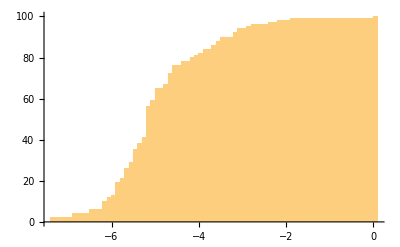

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.36474,0)(-7.36474,1)(-7.36474,2)(-6.84581,3)(-6.84581,4)(-6.40432,5)(-6.40432,6)(-6.18743,7)(-6.18743,8)(-6.1169,9)(-6.1169,10)(-6.03263,11)(-6.03263,12)(-5.99706,13)(-5.89426,14)(-5.89426,15)(-5.83176,16)(-5.83176,17)(-5.80647,18)(-5.80647,19)(-5.79663,20)(-5.79663,21)(-5.62545,22)(-5.622,23)(-5.622,24)(-5.61802,25)(-5.61802,26)(-5.55935,27)(-5.5411,28)(-5.5411,29)(-5.47555,30)(-5.47555,31)(-5.44464,32)(-5.44464,33)(-5.43735,34)(-5.43735,35)(-5.36373,36)(-5.30884,37)(-5.30884,38)(-5.257,39)(-5.22811,40)(-5.22811,41)(-5.19991,42)(-5.19991,43)(-5.18168,44)(-5.18168,45)(-5.17254,46)(-5.17254,47)(-5.17124,48)(-5.17124,49)(-5.13081,50)(-5.13081,51)(-5.1163,52)(-5.10972,53)(-5.10972,54)(-5.10829,55)(-5.10829,56)(-5.09961,57)(-5.09961,58)(-5.05623,59)(-4.98721,60)(-4.98721,61)(-4.97789,62)(-4.97789,63)(-4.92558,64)(-4.92558,65)(-4.76915,66)(-4.76915,67)(-4.67407,68)(-4.61102,69)(-4.61102,70)(-4.60225,71)(-4.60225,72)(-4.57031,73)(-4.57031,74)(-4.50145,75)(-4.50145,76)(-4.39775,77)(-4.39775,78)(-4.16865,79)(-4.16865,80)(-4.06581,81)(-3.92292,82)(-3.82572,83)(-3.82572,84)(-3.6234,85)(-3.6234,86)(-3.5867,87)(-3.5867,88)(-3.42249,89)(-3.42249,90)(-3.19788,91)(-3.19788,92)(-3.02515,93)(-3.02515,94)(-2.88401,95)(-2.70425,96)(-2.38435,97)(-2.12116,98)(-1.86795,99)(0.,100)(0.5,100)

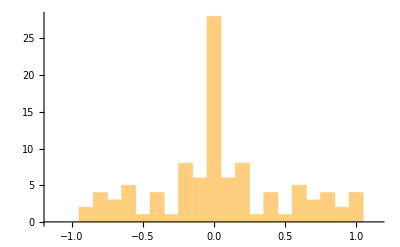

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.926641,1)(-0.916044,2)(-0.844988,3)(-0.821674,4)(-0.788745,5)(-0.756113,6)(-0.747805,7)(-0.703002,8)(-0.680363,9)(-0.618958,10)(-0.608067,11)(-0.603087,12)(-0.581268,13)(-0.556486,14)(-0.475994,15)(-0.422009,16)(-0.39037,17)(-0.371803,18)(-0.369604,19)(-0.328683,20)(-0.246339,21)(-0.237299,22)(-0.22415,23)(-0.207455,24)(-0.183707,25)(-0.172445,26)(-0.152141,27)(-0.151742,28)(-0.13167,29)(-0.10305,30)(-0.0997305,31)(-0.0984826,32)(-0.0857264,33)(-0.0763756,34)(-0.0383161,35)(-0.0368297,36)(-0.0355447,37)(-0.0312495,38)(-0.0291543,39)(-0.0287157,40)(-0.0159479,41)(-0.0155324,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.0155324,55)(0.0159479,56)(0.0287157,57)(0.0291543,58)(0.0312495,59)(0.0355447,60)(0.0368297,61)(0.0383161,62)(0.0763756,63)(0.0857264,64)(0.0984826,65)(0.0997305,66)(0.10305,67)(0.13167,68)(0.151742,69)(0.152141,70)(0.172445,71)(0.183707,72)(0.207455,73)(0.22415,74)(0.237299,75)(0.246339,76)(0.328683,77)(0.369604,78)(0.371803,79)(0.39037,80)(0.422009,81)(0.475994,82)(0.556486,83)(0.581268,84)(0.603087,85)(0.608067,86)(0.618958,87)(0.680363,88)(0.703002,89)(0.747805,90)(0.756113,91)(0.788745,92)(0.821674,93)(0.844988,94)(0.916044,95)(0.926641,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

351

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersTurkish=TopicClusters;
```

```mathematica
Timing[PtrTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{362.859,Null}

```mathematica
Timing[PtrT=Table[v=Table[prepP=PtrTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[PtrT];]
```

{1.28125,Null}

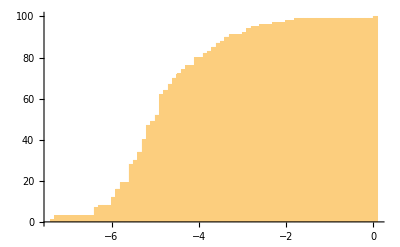

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.35349,0)(-7.35349,1)(-7.25871,2)(-7.25871,3)(-6.38052,4)(-6.38052,5)(-6.3281,6)(-6.3281,7)(-6.24104,8)(-5.98824,9)(-5.97116,10)(-5.9093,11)(-5.9093,12)(-5.89407,13)(-5.89407,14)(-5.88343,15)(-5.88343,16)(-5.763,17)(-5.763,18)(-5.73952,19)(-5.58077,20)(-5.58077,21)(-5.57482,22)(-5.57482,23)(-5.56317,24)(-5.55551,25)(-5.55551,26)(-5.54057,27)(-5.54057,28)(-5.49765,29)(-5.49765,30)(-5.32187,31)(-5.32187,32)(-5.31337,33)(-5.31337,34)(-5.29786,35)(-5.29786,36)(-5.27797,37)(-5.27797,38)(-5.2611,39)(-5.2611,40)(-5.18268,41)(-5.16021,42)(-5.16021,43)(-5.15178,44)(-5.15178,45)(-5.13101,46)(-5.13101,47)(-5.04177,48)(-5.04177,49)(-4.98814,50)(-4.98814,51)(-4.91516,52)(-4.89774,53)(-4.89774,54)(-4.88325,55)(-4.88325,56)(-4.85057,57)(-4.85057,58)(-4.83889,59)(-4.83889,60)(-4.80418,61)(-4.80418,62)(-4.74751,63)(-4.74751,64)(-4.63396,65)(-4.60157,66)(-4.60157,67)(-4.56145,68)(-4.56145,69)(-4.50645,70)(-4.41784,71)(-4.41784,72)(-4.30483,73)(-4.30483,74)(-4.23351,75)(-4.23351,76)(-4.09385,77)(-4.09385,78)(-4.06336,79)(-4.06336,80)(-3.82845,81)(-3.82845,82)(-3.70595,83)(-3.61812,84)(-3.61812,85)(-3.52948,86)(-3.52948,87)(-3.44794,88)(-3.30023,89)(-3.30023,90)(-3.20595,91)(-2.97457,92)(-2.89096,93)(-2.89096,94)(-2.77868,95)(-2.57878,96)(-2.29324,97)(-1.99195,98)(-1.73535,99)(0.,100)(0.5,100)

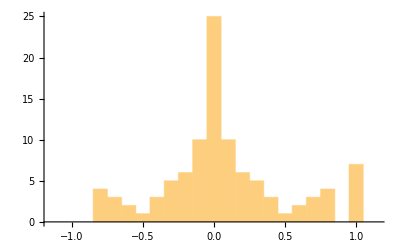

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.848714,1)(-0.84454,2)(-0.832473,3)(-0.755659,4)(-0.737558,5)(-0.689076,6)(-0.654485,7)(-0.645189,8)(-0.554626,9)(-0.547908,10)(-0.436938,11)(-0.405638,12)(-0.382377,13)(-0.316328,14)(-0.315284,15)(-0.309553,16)(-0.29987,17)(-0.293519,18)(-0.249193,19)(-0.243847,20)(-0.237407,21)(-0.230083,22)(-0.206514,23)(-0.165487,24)(-0.137475,25)(-0.134707,26)(-0.13468,27)(-0.12449,28)(-0.111625,29)(-0.100453,30)(-0.0985429,31)(-0.0980476,32)(-0.0611077,33)(-0.0515571,34)(-0.0470751,35)(-0.0448093,36)(-0.032863,37)(-0.0279113,38)(-0.0143577,39)(-0.00637725,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.00637725,54)(0.0143577,55)(0.0279113,56)(0.032863,57)(0.0448093,58)(0.0470751,59)(0.0515571,60)(0.0611077,61)(0.0980476,62)(0.0985429,63)(0.100453,64)(0.111625,65)(0.12449,66)(0.13468,67)(0.134707,68)(0.137475,69)(0.165487,70)(0.206514,71)(0.230083,72)(0.237407,73)(0.243847,74)(0.249193,75)(0.293519,76)(0.29987,77)(0.309553,78)(0.315284,79)(0.316328,80)(0.382377,81)(0.405638,82)(0.436938,83)(0.547908,84)(0.554626,85)(0.645189,86)(0.654485,87)(0.689076,88)(0.737558,89)(0.755659,90)(0.832473,91)(0.84454,92)(0.848714,93)(1.,94)(1.,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
TurkishRef=TopicClustersTurkish;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapTurkish=StringReplace[ImportString[#,"HTML"]&/@StringReplace[StringReplace[StringReplace[StringSplit[Import["Pride and Prejudice (Turkish).txt"],"BÖLÜM"],{"I":>"ı","İ":>"i","\n":>"\n舜"}],{(s:("舜"~~Repeated[Except["\n"],{1,80}]))~~"\n":>s<>"垚"}],{"舜":>""}],{"垚":>"\n\n"}];
```

```mathematica
Length[PandPChapTurkish]
```

61

```mathematica
VecTurkish=Table[{TurkishRef_⟦k,1⟧,StringCount[PandPChapTurkish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@TurkishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[TurkishRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecTurkish,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100 √61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedTurkishRef=Reverse[SortBy[Table[Cases[TurkishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

96

```mathematica
Length[SiftedTurkishRef]
```

96

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{48.0412,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Turkish

```mathematica
ToTopicsTurkish=SiftedTurkishRef;
```

```mathematica
Length[ToTopicsTurkish]
```

96

```mathematica
ToDeltaTurkish=ReadDelta[#]&/@ToTopicsTurkish;
```

```mathematica
ToNTurkish=(#_⟦3⟧-1)&/@ToTopicsTurkish;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersTurkish,PtrTopic,#_⟦1⟧&/@ToTopicsTurkish];]
```

{238.714,Null}

```mathematica
ToKinTurkish=KinQ;
```

```mathematica
ToEtaTurkish=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsTurkish,ToKinTurkish}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.0229163,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{Brighton,24}}->{{brighton,5},{brighton♯a,12},{brighton♯da,2},{brighton♯daki,1},{brighton♯dan,4}}
0.8340288641686 | 1 | 1
{{Bourgh,35},{Bourgh's,4}}->{{bourgh,19},{bourgh♯a,3},{bourgh♯dan,1},{bourgh♯du,1},{bourgh♯tan,1},{bourgh♯u,2},{bourgh♯un,14}}
0.78335220278022 | 1 | 1
{{impossible,44}}->{{imkânsız,24},{imkânsızdı,13},{imkânsızdır,2},{imkânsızlaşır,1},{imkânsızlığın,1},{imkânsızlıklarına,1}}
0.78629569721068 | 1 | 1
{{library,23}}->{{kütüphanede,1},{kütüphaneden,1},{kütüphanem,1},{kütüphanemin,1},{kütüphanemizde,1},{kütüphaneye,7},{kütüphaneyi,1},{kütüphanemde,1},{kütüphaneniz,1},{kütüphanesinin,1},{kütüphanesinde,4},{kütüphanesinden,2},{kütüphanesindeki,1},{kütüphanesine,3}}
0.82470720351874 | 1 | 1
{{London,55}}->{{londra,2},{londra♯da,12},{londra♯daki,2},{londra♯dalar,1},{londra♯dan,11},{londra♯nın,6},{londra♯ya,21}}
0.80764437883449 | 1 | 1
{{Meryton,57}}->{{meryton,6},{meryton♯a,20},{meryton♯da,12},{meryton♯daki,7},{meryton♯dan,8},{meryton♯daydı,1},{meryton♯un,3}}
0.88847813275632 | 1 | 1
{{money,26}}->{{parça,8},{parmağı,1},{parmaklarım,2},{parmaklarımda,1},{parmaklarında,1},{parti,1},{partiler,3},{para,14},{param,1},{paramız,1},{paramızı,1},{paranın,1},{paranızın,1},{parası,6},{parasıyla,1},{parasına,1},{parasını,1}}
0.89586101210736 | 1 | 1
{{Mr,786}}->{{mr,977}}
0.7366399814233 | 1 | 1
{{Mrs,343}}->{{mrs,372}}
0.92460908562146 | 1 | 1
{{Netherfield,73}}->{{netherfield,13},{netherfield♯a,15},{netherfield♯da,18},{netherfield♯daki,5},{netherfield♯dakileri,1},{netherfield♯dan,11},{netherfield♯dayken,1},{netherfield♯ı,3},{netherfield♯ın,3},{netherfield♯lı,2}}
0.86640345944054 | 1 | 1
{{oh,95}}->{{ah,83},{ahmak,12},{ahmakça,3},{ahmaklığı,4},{ahmaklığına,2},{ahmaklığını,1},{ahmaklık,5},{ahmaklıklar,1},{ahmaklıklara,1},{ahmaklıkları,2},{ahmaklıklarına,1},{ahmaklıklarını,1},{ahmaklıktan,1},{ahmaklıktaydı,1},{ahmaksa,1},{ahmaktı,1}}
0.81641147643239 | 1 | 1
{{Pemberley,53}}->{{pemberley,11},{pemberley♯de,9},{pemberley♯deki,4},{pemberley♯den,2},{pemberley♯deydi,1},{pemberley♯e,12},{pemberley♯i,8},{pemberley♯in,6}}
0.77234860561008 | 1 | 1
{{pounds,24}}->{{poundu,2},{poundun,2},{pound,16},{pounddan,6},{poundluk,2}}
0.9107891555868 | 1 | 1
{{Rosings,49}}->{{rosings,6},{rosings♯e,13},{rosings♯in,3},{rosings♯le,3},{rosings♯te,7},{rosings♯teki,13},{rosings♯tekilerin,1},{rosings♯ten,3}}
0.83282216439884 | 1 | 1
{{sir,78}}->{{william,37},{william♯a,2},{william♯ı,1},{william♯ın,8},{william♯larda,1}}
0.91602412258323 | 1 | 2
{{William,40},{William's,6}}->{{sir,52}}
0.91545202629132 | 2 | 1
{{ball,34},{balls,8}}->{{balo,18},{baloda,7},{balodan,3},{balolar,3},{balolarda,3},{balolarımızı,1},{baloların,1},{balolarla,1},{balonun,6},{baloya,5},{baloydu,1},{baloyu,2},{balonuzu,1},{balosunun,1},{balosu,2},{balosunda,2},{balosuna,2},{balosundaki,2}}
0.8199102557312 | 1 | 1
{{Catherine,110},{Catherine's,16}}->{{lady,144},{lady♯nin,3}}
0.91847578949063 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{charlotte,53},{charlotte♯a,10},{charlotte♯la,1},{charlotte♯tan,2},{charlotte♯u,5},{charlotte♯uma,1},{charlotte♯umun,1},{charlotte♯un,32},{charlotte♯undan,1},{charlotte♯unun,1}}
0.89176310372593 | 1 | 1
{{civilities,7},{civility,42}}->{{nezakete,2},{nezaketi,2},{nezaketin,3},{nezaket,16},{nezaketten,3},{nezaketinde,1},{nezaketinden,1},{nezaketine,4},{nezaketini,1},{nezaketle,18}}
0.85681649863473 | 1 | 1
{{Collins,156},{Collins's,24}}->{{collins,144},{collins♯e,16},{collins♯i,14},{collins♯in,64},{collins♯le,6},{collins♯ler,2},{collins♯lere,1},{collins♯lerin,2},{collins♯te,1},{collins♯ten,7},{collıns,1}}
0.83017586399379 | 1 | 1
{{father,116},{father's,19}}->{{baba,5},{babadan,1},{babaları,8},{babalarına,6},{babalarında,1},{babalarının,5},{babam,20},{babama,5},{babamın,12},{babamızın,1},{baban,5},{babanın,4},{babayla,1},{babana,2},{babanı,1},{babanız,2},{babanızdan,1},{babanızın,4},{babanızla,1},{babanla,1},{babasının,34},{babası,32},{babasından,4},{babasıyla,5},{babasına,8},{babasını,5}}
0.88837671904655 | 1 | 1
{{four,33},{four-and-twenty,1}}->{{dördünün,1},{dört,33},{dörtte,2}}
0.87063988770152 | 1 | 1
{{Jane,263},{Jane's,28}}->{{jane,172},{jane♯den,16},{jane♯di,1},{jane♯e,38},{jane♯i,21},{jane♯im,1},{jane♯imi,1},{jane♯in,94},{jane♯inki,2},{jane♯le,5}}
0.84172918612521 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitty,56},{kitty♯nin,9},{kitty♯ye,5},{kitty♯yi,1},{kitty♯yle,2}}
0.85927367166346 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{lizzy,81},{lizzy♯de,1},{lizzy♯den,1},{lizzy♯m,1},{lizzy♯nin,5},{lizzy♯ye,2},{lizzy♯yi,3},{lizzy♯yle,2}}
0.86353499081888 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lydia,103},{lydia♯cığım,1},{lydia♯dan,4},{lydia♯ma,2},{lydia♯nın,82},{lydia♯ya,11},{lydia♯ydı,1},{lydia♯yı,7},{lydia♯yla,1}}
0.86112986550254 | 1 | 1
{{Mary,38},{Mary's,1}}->{{mary,35},{mary♯nin,3},{mary♯ye,1},{mary♯yi,2}}
0.79578395531159 | 1 | 1
{{room,112},{rooms,8}}->{{oda,6},{odada,19},{odadan,18},{odalar,1},{odalara,2},{odalardan,1},{odaları,1},{odalarımızla,1},{odaların,2},{odalarına,4},{odalarında,1},{odalarındaki,1},{odalarını,1},{odam,1},{odama,1},{odanın,2},{odaya,25},{odaydı,2},{odayı,4},{odanız,1},{odasının,3},{odası,5},{odasında,12},{odasından,8},{odasıyla,2},{odasına,27},{odasındaki,3}}
0.75933457236408 | 1 | 1
{{serious,24},{seriously,13}}->{{cidden,7},{ciddi,37}}
0.81884296476759 | 1 | 1
{{table,28},{tables,3}}->{{masum,2},{masa,2},{masada,3},{masadan,2},{masalar,1},{masalara,1},{masaları,4},{masanın,7},{masaya,7},{masayı,1},{masası,3},{masasından,1},{masasına,4},{masasını,2}}
0.85244499209265 | 1 | 1
{{week,29},{weeks,18}}->{{hafta,43}}
0.81674031668318 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{wickham,103},{wickham♯a,23},{wickham♯dan,6},{wickham♯ı,22},{wickham♯ımdaydı,1},{wickham♯ın,94},{wickham♯ıydı,1},{wickham♯la,19}}
0.83175612890876 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennet,245},{bennet♯a,23},{bennet♯ı,15},{bennet♯ın,66},{bennet♯la,5},{bennet♯lar,4},{bennet♯ların,5},{bennet♯tan,5}}
0.89023583592217 | 1 | 1
{{child,14},{children,25},{childhood,1}}->{{çocuğum,4},{çocuğunun,2},{çocuk,4},{çocuklar,2},{çocukları,5},{çocuklarım,1},{çocuklarıma,1},{çocukların,1},{çocuklarına,2},{çocuklarının,5},{çocuklarınız,2},{çocuklarınızı,1},{çocuklarıyla,1},{çocuklarla,2},{çocuktu,1},{çocukken,4},{çocukluk,1},{çocukluğumuzun,1},{çocukluğundan,1},{çocuğu,2},{çocuğuydu,1},{çocuğumla,1},{çocuğunu,1},{çocuğunuzu,1}}
0.78318755634369 | 1 | 1
{{cousin,41},{cousin's,8},{cousins,11}}->{{kuzum,1},{kuzen,1},{kuzenim,10},{kuzeniniz,2},{kuzeninkinden,1},{kuzenleri,3},{kuzenlerime,1},{kuzenlerimin,2},{kuzenlerinden,1},{kuzenlerine,3},{kuzenlerini,1},{kuzenlerinin,2},{kuzenleriyse,1},{kuzeye,3},{kuzey♯de,1},{kuzey♯e,4},{kuzeninin,13},{kuzeni,6},{kuzenime,3},{kuzenimi,2},{kuzenimin,3},{kuzenimize,1},{kuzeniymiş,1},{kuzenine,5},{kuzenini,6},{kuzeninizin,1},{kuzeninize,1}}
0.90760005848096 | 1 | 1
{{dear,158},{dearly,3},{dearest,17}}->{{sevgili,100},{sevgilisinin,1},{sevgilisiydi,1}}
0.76721417668013 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{akşam,68},{akşama,5},{akşamı,6},{akşamın,7},{akşamına,1},{akşamında,1},{akşamkinden,1},{akşamlardı,1},{akşamları,3}}
0.85953575877358 | 1 | 1
{{eye,15},{eyeing,1},{eyes,52}}->{{göz,32},{gözde,2},{gözden,4},{gözlere,2},{gözleri,9},{gözlerim,1},{gözlerimle,1},{gözlerin,2},{gözlerinde,3},{gözlerindeki,1},{gözlerine,7},{gözlerini,13},{gözlerinin,3},{gözleriyle,3},{gözlerle,1},{gözün,1},{gözünün,1}}
0.83398500614453 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{forster,22},{forster♯a,8},{forster♯dan,3},{forster♯ın,3},{forster♯la,2},{forster♯lar,1},{forster♯larda,1}}
0.78625250391729 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{gardiner,69},{gardiner♯den,4},{gardiner♯e,4},{gardiner♯i,3},{gardiner♯in,19},{gardiner♯lardan,1},{gardiner♯le,1},{gardiner♯ler,5}}
0.87105725084428 | 1 | 1
{{husband,42},{husband's,8},{husbands,4}}->{{kocam,1},{kocan,1},{kocaya,2},{kocayla,1},{kocanı,2},{kocasının,17},{kocası,11},{kocasından,1},{kocasıyla,3},{kocasını,1}}
0.87756203530757 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{mektubum,1},{mektubun,13},{mektubunun,5},{mektuba,3},{mektubu,56},{mektubuma,2},{mektubunda,7},{mektubundan,1},{mektubumda,1},{mektubuna,5},{mektubunu,15},{mektubunuza,1},{mektubunuzdakinden,1},{mektuplaşmaktan,1},{mektuplar,6},{mektuplarda,2},{mektuplardan,3},{mektupları,7},{mektuplarımdan,1},{mektupların,1},{mektuplarından,1},{mektuplarla,2},{mektupta,5},{mektuptan,3},{mektupla,3}}
0.75326420826001 | 1 | 1
{{young,130},{younger,30},{youngest,13}}->{{gencin,1},{genç,189},{gençler,2},{gençleri,2},{gençlerin,2}}
0.8185243078653 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{anne,14},{anneleri,6},{annelerine,3},{annelerini,2},{annelerinin,12},{annem,8},{anneme,2},{annemin,6},{annemiz,1},{annen,3},{anneye,1},{anneyi,1},{anneyle,2},{anne♯e,1},{anne♯in,1},{annene,1},{anneniz,6},{annenizin,3},{annenize,2},{annenizi,1},{annesinin,36},{annesi,41},{annesinden,1},{annesiyle,5},{annesine,8},{annesini,4},{annesley,2},{annesley♯in,1}}
0.88165932993178 | 1 | 1
{{niece,20},{niece's,2},{nieces,9}}->{{yeğen,2},{yeğenden,1},{yeğenim,10},{yeğeniniz,1},{yeğenleri,3},{yeğenlerine,6},{yeğenlerini,2},{yeğenlerinin,2},{yeğenleriyle,1},{yeğeninin,4},{yeğeni,11},{yeğenimin,4},{yeğeninden,1},{yeğeniyle,2},{yeğenine,6},{yeğenini,1},{yeğeninizin,2},{yeğeninizle,2},{yeğenle,1}}
0.7166969080842 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{phillips,19},{phillips♯e,3},{phillips♯i,2},{phillips♯in,11},{phillips♯ler,1},{phillips♯lere,1},{phillips♯lerin,1},{phillips♯ten,2}}
0.84816374563212 | 1 | 1
{{read,40},{reading,14},{reader,3}}->{{oku,1},{okudu,7},{okuduklarımdan,1},{okuduğu,5},{okuduğunda,7},{okuma,1},{okumadığımıza,1},{okumadığını,1},{okumak,3},{okumakta,1},{okumaktan,1},{okumasını,1},{okumaya,12},{okumayı,2},{okumuş,1},{okumuşken,1},{okuyabileceği,1},{okuyabiliyordu,1},{okuyabilmesi,1},{okuyacağım,1},{okuyacak,1},{okuyordu,1},{okuyup,4},{okundu,1},{okusam,1},{okusak,1}}
0.78532502287985 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{amcam,1},{amcanız,1},{amcanızın,1},{amcası,1},{amcasının,1},{dayıları,4},{dayılarının,1},{dayılarınız,1},{dayılarıyla,1},{dayım,9},{dayımdan,2},{dayımı,3},{dayımın,6},{dayımız,1},{dayımla,4},{dayın,5},{dayına,1},{dayının,2},{dayınız,1},{dayınızın,1},{dayınla,2},{dayınsa,1},{dayısı,18},{dayısına,1},{dayısından,1},{dayısını,1},{dayısının,8}}
0.87047882925348 | 1 | 1
{{wife,44},{wife's,3},{wives,1}}->{{karısının,9},{karısınınkinden,1},{karısı,14},{karısından,1},{karısına,6},{karısını,2}}
0.88049894815855 | 1 | 1
{{year,28},{years,33},{years',2}}->{{yıl,18},{yılda,12},{yıldır,1},{yılın,4},{yılkinden,1},{yıllar,6},{yıllarca,3},{yıllardır,2},{yıllarında,2}}
0.91182015154004 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{bingley,232},{bingley♯de,1},{bingley♯den,9},{bingley♯dir,1},{bingley♯e,22},{bingley♯i,25},{bingley♯imizin,1},{bingley♯in,146},{bingley♯inkiler,1},{bingley♯le,4},{bingley♯ler,1},{bingley♯lerden,1},{bingley♯lere,1},{bingley♯leri,1}}
0.80982140301489 | 1 | 1
{{character,64},{characters,3},{characteristic,2},{characterise,1}}->{{karakter,3},{karakterim,3},{karakterinin,8},{karakteriniz,2},{karakterler,1},{karakterlere,1},{karakterleri,1},{karakterlerin,1},{karakterlerinin,3},{karakterleriniz,1},{karakterde,2},{karakterdi,1},{karaktere,1},{karakteri,23},{karakterime,1},{karakterimi,4},{karakterimin,1},{karakterinde,1},{karakterinden,2},{karakteriyle,1},{karakterindeki,2},{karakterine,11},{karakterini,14},{karakterinize,1},{karakterinizi,3}}
0.80763607168775 | 1 | 1
{{complied,4},{compliment,26},{compliments,11},{compliance,1}}->{{iltifata,1},{iltifatı,4},{iltifatın,3},{iltifat,14},{iltifatlar,6},{iltifatlarda,1},{iltifatları,1},{iltifatların,1},{iltifatlarını,2},{iltifatlarıyla,1},{iltifattan,1},{iltifattı,1},{iltifatında,1}}
0.90010213124669 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{güce,1},{gün,129},{günde,2},{günden,10},{günler,2},{günleri,5},{günlerinin,1},{günün,11}}
0.89577986514395 | 1 | 1
{{dance,31},{danced,12},{dances,10},{dancing,21}}->{{dans,78},{danslar,1},{danslardı,1},{dansları,2},{danslarına,1},{danslarındaki,1},{dansta,6}}
0.74348273447364 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucas,40},{lucas♯a,7},{lucas♯ı,6},{lucas♯ın,18},{lucas♯ınkinden,1},{lucas♯la,3},{lucas♯lar,4},{lucas♯lara,2},{lucas♯larda,2},{lucas♯lardan,1},{lucas♯ları,1},{lucas♯ların,1},{lucas♯larla,1}}
0.87604239164924 | 1 | 1
{{said,401},{say,160},{saying,35},{says,15}}->{{dedi,306},{dediği,1},{dediğim,4},{dediğimi,2},{dediğin,2},{dediğine,3},{dediğini,4},{dediğiniz,2},{dediğinizi,2},{dedikodu,1},{dedikoducu,1},{dedikodular,1},{dedikoduları,1},{dedikoduların,1},{dedikodularından,1},{dedikodusu,1},{dedikodusunu,1},{dedikoduya,1},{dedikoduyu,1},{dedim,4},{dediniz,1},{dedirtmeyecekti,1},{deme,1},{demeden,1},{demedi,7},{demedim,1},{demek,34},{demekten,1},{demektir,7},{demeli,1},{demeliydi,1},{demeliyim,1},{demem,3},{dememesine,1},{dememi,1},{demesini,1},{demeye,1},{demiş,2},{demişimdir,1},{demişti,1},{demiştiniz,1},{den,1},{dendiğinde,1},{denebilecek,1},{denebilir,1},{denmiş,1},{der,2},{derdi,1},{derdim,1},{derim,5},{derin,15},{derman,1},{dersin,2},{dersiniz,1},{deyip,2},{diyeceği,1},{diyeceğim,1},{diyeceğimi,1},{diyeceğini,1},{diyeceğiniz,1},{diyecek,1},{diyeceksiniz,1},{diyor,4},{diyordu,8},{diyorduk,1},{diyordum,1},{diyorlar,1},{diyorsun,2},{diyorsunuz,1},{diyorum,2}}
0.8187989198409 | 1 | 1
{{admire,18},{admired,12},{admires,2},{admiring,2},{admirer,3}}->{{hayran,14},{hayranlarından,1},{hayrandı,2},{hayranının,1},{hayranı,1},{hayranıydı,1},{hayranlığın,1},{hayranlığı,1},{hayranlığından,1},{hayranlığına,1},{hayranlığını,4},{hayranlığınızı,1},{hayranlık,17},{hayranlıklarını,1},{hayranlıkla,8}}
0.8293488832368 | 1 | 1
{{believed,37},{believing,12},{belief,15},{believe,87},{believes,1}}->{{inan,3},{inanabilirdi,1},{inanabilirim,1},{inanabiliyor,1},{inanacak,1},{inandığım,2},{inandığına,1},{inandığını,2},{inandıktan,1},{inanın,5},{inanınız,4},{inanıp,1},{inanma,3},{inanmadı,1},{inanmadığı,1},{inanmadığınızı,1},{inanmak,7},{inanmakta,3},{inanmaktan,2},{inanmam,3},{inanmama,1},{inanmamakta,1},{inanmamayı,1},{inanmamın,1},{inanman,1},{inanmanız,1},{inanmasa,1},{inanmasaydı,1},{inanmasaymış,1},{inanması,1},{inanmasına,2},{inanmaya,5},{inanmayacağına,1},{inanmayacak,2},{inanmaz,2},{inanmazdı,2},{inanmazsın,1},{inanmış,1},{inanmıştım,1},{inanmıyor,1},{inanmıyordu,2},{inanmıyorsan,1},{inanmıyorsun,1},{inanmıyorum,2},{inandı,1},{inandınız,2},{inandırıcı,1},{inandırmak,2},{inandırmaya,1},{inandırmışken,1},{inandırsaydım,1},{inanamam,2},{inanamayan,1},{inanamazdı,1},{inanamazsınız,2},{inanamıyor,1},{inanamıyordu,1},{inanamıyorsanız,1},{inanamıyorum,4},{inanan,1},{inanarak,2},{inancının,2},{inançlarımın,1},{inancı,2},{inancıyla,1},{inancını,2},{inançla,3},{inandıysanız,1},{inanır,1},{inanırım,4},{inanırsınız,1},{inanıyor,3},{inanıyordu,10},{inanıyordum,1},{inanıyordunuz,1},{inanıyormuş,1},{inanıyorsanız,1},{inanıyorsun,1},{inanıyorum,14},{inanılmaz,4},{inanılmazdı,1},{inanırken,1},{inansa,1},{inansalardı,1},{inansam,1}}
0.71982932653113 | 1 | 1
{{carriage,44},{carriages,6},{carried,8},{carry,5},{carrying,4}}->{{araba,20},{arabada,1},{arabadan,3},{arabalar,2},{arabaları,1},{arabaların,3},{arabalarına,1},{arabalarından,1},{arabalarını,1},{arabalarının,1},{arabanın,12},{arabaya,9},{arabayı,5},{arabayla,2},{arabacının,2},{arabasının,4},{arabası,6},{arabasından,1},{arabasıyla,2},{arabasını,3}}
0.80932560098472 | 1 | 1
{{congratulate,7},{congratulated,2},{congratulation,1},{congratulations,12},{congratulatory,1}}->{{tebrik,14},{tebrikler,2},{tebrikleri,4},{tebriklerimi,1},{tebriklerini,3},{tebriklerinizi,1},{tebriklerle,1}}
0.86710055682799 | 1 | 1
{{console,9},{consoled,2},{consoling,3},{consolation,10},{consolatory,1}}->{{tesellim,1},{teselli,32},{teselliydi,1},{tesellisinin,1},{tesellisi,2},{tesellisiydi,1}}
0.78303093081669 | 1 | 1
{{differ,1},{different,36},{differently,7},{difference,10},{differences,1}}->{{farklı,34},{farklıdır,1},{farklıydı,1}}
0.71268580953137 | 1 | 1
{{disappoint,2},{disappointed,12},{disappointing,3},{disappointment,17},{disappointments,1}}->{{kırık,1},{kırıklığının,1},{kırıklığı,7},{kırıklığıydı,1},{kırıklığına,18},{kırıklığını,3},{kırıklıkları,1},{kırıklıklarına,1}}
0.85946770052999 | 1 | 1
{{invite,6},{invited,11},{inviting,3},{invitation,34},{invitations,1}}->{{davet,46},{davetinin,1},{davetler,1},{davetlerde,1},{davetlerden,1},{davetleri,1},{davetlerin,1},{davetlerini,1},{davetti,1},{davetiye,3},{davetiyelerde,1},{davetiyeleri,1},{davetini,3},{davetiyede,1}}
0.80712426407268 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{miss,294}}
0.81145815182102 | 1 | 1
{{pain,28},{painful,14},{painfully,2},{paining,1},{pains,4}}->{{acı,44},{acılar,4},{acılara,1},{acıları,2},{acıların,2},{acılarına,1},{acılarını,1},{acımanız,1},{acımaz,1},{acımızı,1},{acıydı,2},{acıyla,3},{acıyorum,1},{acınası,3},{acınızı,1},{acısaydı,1},{acısı,2},{acısından,1},{acısını,4}}
0.74478033131836 | 1 | 1
{{pride,47},{prided,1},{proud,22},{proudly,1},{proudest,1}}->{{gururdan,2},{gururla,1},{gururlu,16},{gururu,18},{gururudur,1},{gururunda,1},{gururundan,1},{gururunu,5},{gururunuzu,1}}
0.87069843225733 | 1 | 1
{{refuse,9},{refused,6},{refusing,7},{refusal,7},{refusals,1}}->{{reddedemezsiniz,1},{reddederek,3},{reddederken,3},{reddedersen,1},{reddediyorsunuz,2},{reddedildi,2},{reddedilmediği,1},{reddedilmiş,1},{reddedilemeyeceği,1},{reddedilen,1},{reddetmede,1},{reddetmek,2},{reddetmekten,1},{reddetmeleri,1},{reddetmem,1},{reddetmeni,1},{reddetmenizde,1},{reddetmenize,1},{reddetmenizi,1},{reddetmenizle,1},{reddetmesi,2},{reddetmesinin,1},{reddetmeyi,2},{reddetmezseniz,1},{reddetmişsin,1},{reddetti,6},{reddettiğim,2},{reddettiğini,1},{reddettikleri,1}}
0.85536455581809 | 1 | 1
{{saw,103},{see,149},{seeing,60},{seen,76},{sees,6}}->{{gör,6},{gördü,33},{gördükleri,4},{gördüklerim,1},{gördüklerimi,1},{gördüklerimizi,1},{gördüklerinde,1},{gördüklerinden,1},{gördükten,3},{gördüler,5},{gördüm,10},{gördünüz,4},{gördüğü,17},{gördüğüm,10},{gördüğümde,4},{gördüğüme,1},{gördüğümü,1},{gördüğümüz,2},{gördüğümüzü,1},{gördüğünde,4},{gördüğünden,4},{gördüğüne,5},{gördüğünü,7},{gördüğünüzde,1},{görebildiğimi,1},{görebildiler,1},{görebileceği,1},{görebileceğiniz,1},{görebilirdi,1},{görebilirim,1},{görebilirsin,1},{görebilirsiniz,1},{görebiliyordu,4},{görebiliyorsam,1},{görebilme,1},{görebilseydim,2},{göreceği,1},{göreceğim,2},{göreceğimden,1},{göreceğime,2},{göreceğine,1},{göreceğini,2},{göreceğinize,1},{göreceğiz,1},{görecek,4},{göreceklerine,1},{göreceksin,1},{göreceksiniz,2},{görecekti,1},{görecektir,3},{görme,21},{görmedi,1},{görmediği,2},{görmediğimi,1},{görmediğinden,1},{görmediğini,4},{görmedikleri,1},{görmediler,1},{görmedim,9},{görmek,26},{görmekten,13},{görmeleri,2},{görmelerine,1},{görmelerini,1},{görmelerinin,1},{görmeme,1},{görmemesi,1},{görmemiş,3},{görmemişlerdi,1},{görmemişti,7},{görmemiştim,5},{görmemiştiniz,1},{görmemiştir,1},{görmemiz,1},{görmen,1},{görmenin,1},{görmenizi,1},{görmese,1},{görmesem,1},{görmeseydi,1},{görmesi,1},{görmesine,3},{görmesini,1},{görmesinin,2},{görmesiyle,2},{görmeye,14},{görmeyen,1},{görmeyi,5},{görmezden,4},{görmezsiniz,1},{görmüş,11},{görmüşler,1},{görmüşlerdi,4},{görmüşsündür,1},{görmüşsünüz,1},{görmüşsünüzdür,2},{görmüştü,10},{görmüyorlarmış,1},{görmüyorsun,1},{görmüyorum,1},{görsün,1},{görün,1},{görünce,22},{göründüklerine,1},{göründüklerini,1},{göründüğü,1},{göründüğüne,1},{göründüğünü,5},{göründüğünün,1},{görünecektir,2},{görünmeden,1},{görünmedi,2},{görünmediğini,1},{görünmediklerini,1},{görünmek,2},{görünmekte,1},{görünmelerine,1},{görünmem,1},{görünmemek,2},{görünmemesi,1},{görünmemeye,1},{görünmese,1},{görünmesi,1},{görünmesini,1},{görünmesiyle,1},{görünmeye,3},{görünmeyen,1},{görünmeyi,1},{görünmüştü,4},{görünmüyor,1},{görünmüyordu,7},{görünmüyorsun,1},{görünmüyorsunuz,1},{görünüm,1},{görününce,1},{görünüp,1},{görünüz,2},{görüp,19},{göremem,2},{görememen,1},{göremeyeceği,1},{göremeyecek,1},{göremiyorlardı,1},{göremiyorsa,1},{göremiyorum,2},{gören,15},{görenlere,1},{göreydi,1},{göreyim,1},{göresim,1}}
0.8253435898927 | 1 | 1
{{serve,2},{serving,1},{servant,15},{servant's,2},{servants,12}}->{{hizmetçi,11},{hizmetçiler,6},{hizmetçileri,1},{hizmetçilerin,3},{hizmetçilerinin,1},{hizmetçilerle,1},{hizmetçimiz,1},{hizmetçinin,7},{hizmetçinizi,1},{hizmetçisi,2},{hizmetçisine,1},{hizmetçisinin,2},{hizmetçiye,1},{hizmetimize,1},{hizmetini,1},{hizmetli,3}}
0.89884194160442 | 1 | 1
{{feel,39},{feeling,38},{feelingly,1},{feelings,86},{feels,4},{felt,100}}->{{his,2},{hisler,15},{hislerde,1},{hislere,3},{hisleri,30},{hislerim,3},{hislerimden,2},{hislerime,2},{hislerimi,6},{hislerimin,2},{hislerimizin,1},{hislerin,5},{hislerinde,3},{hislerindeki,3},{hislerinden,6},{hislerine,4},{hislerini,19},{hislerinin,10},{hisleriniz,4},{hislerinizi,2},{hislerinizin,1},{hislerle,8},{hissin,1},{hisseden,5},{hissedebiliyordu,1},{hissedebilseydim,1},{hissedeceğim,1},{hissedeceğini,1},{hissedecek,1},{hissedeceksin,1},{hissedemez,1},{hissedeyim,1},{hissederdi,1},{hissederek,1},{hissederken,1},{hissederseniz,1},{hissediyor,3},{hissediyordu,14},{hissediyorsa,1},{hissediyorsundur,1},{hissediyorum,5},{hissedildi,1},{hissedilecek,1},{hissedilmesi,1},{hissedinceye,1},{hissetmeden,3},{hissetmediği,3},{hissetmediğime,1},{hissetmediğimize,1},{hissetmediğinden,1},{hissetmek,1},{hissetmekle,1},{hissetmekte,1},{hissetmem,1},{hissetmemesini,2},{hissetmemiş,1},{hissetmemişti,1},{hissetmen,1},{hissetmenize,1},{hissetmesine,4},{hissetmeye,1},{hissetmez,1},{hissetmiş,1},{hissetmişti,3},{hissetmiştir,1},{hissetmiyor,1},{hissetmiyorum,1},{hissetti,20},{hissettiği,12},{hissettiğim,3},{hissettiğimden,1},{hissettiğime,1},{hissettiğimi,3},{hissettiğinden,2},{hissettiğine,1},{hissettiğini,5},{hissettiğiniz,1},{hissettikleri,1},{hissettiklerinden,1},{hissettiklerini,2},{hissettim,1},{hissettirdiği,1},{hissettirmişti,1},{hissi,1},{hissiyle,4},{hissini,1},{hissinizden,1},{hissiyatla,1}}
0.71201515671101 | 1 | 1
{{forget,17},{forgetfulness,1},{forgets,1},{forgetting,2},{forgot,5},{forgotten,12}}->{{unutabilir,1},{unutabilirdi,1},{unutacağım,1},{unutma,3},{unutmadan,1},{unutmadığınızı,1},{unutmadım,2},{unutmalıyız,1},{unutmama,1},{unutmamalısın,1},{unutmamalısınız,1},{unutmamıştı,1},{unutmamıştır,1},{unutmaya,4},{unutmayacağım,1},{unutmayalım,1},{unutmayı,1},{unutmayınız,1},{unutmuş,2},{unutmuyor,1},{unuttu,2},{unuttuklarını,1},{unuttum,1},{unutturacak,2},{unutturmamıştı,1},{unutturmuş,1},{unutup,1},{unutamayacağım,1},{unutamıyordu,1},{unutamıyorum,1},{unutuyorsun,1},{unutuyorsunuz,1},{unutulacağını,1},{unutuldu,1},{unutulmalıdır,1},{unutulmaması,1},{unutulmamıştı,1},{unutulmuş,1},{unutulup,1},{unutulamaz,1},{unutulsa,1},{unutuvermiş,1},{unutuveriyor,1},{unutuverirdi,1}}
0.75900191674587 | 1 | 1
{{marriage,66},{married,61},{marry,42},{marrying,23},{matrimonial,1},{matrimony,6}}->{{evlendiği,2},{evlendiğimi,1},{evlendiğimizde,1},{evlendiğinde,1},{evlendikleri,2},{evlendiklerinden,1},{evlenebileceğini,1},{evlenebilecekken,1},{evleneceği,1},{evleneceğim,1},{evleneceğime,1},{evleneceğinden,1},{evleneceğine,4},{evleneceğini,1},{evlenecek,5},{evlenecekler,1},{evleneceklerinden,1},{evleneceklerine,1},{evleneceklerini,1},{evleneceksin,1},{evlenip,1},{evlenme,14},{evlenmeden,1},{evlenmediğini,1},{evlenmediklerini,1},{evlenmek,5},{evlenmekle,1},{evlenmeleri,3},{evlenmelerini,1},{evlenmeli,1},{evlenmemde,1},{evlenmemişken,1},{evlenmemişler,1},{evlenmemişlerse,1},{evlenmen,1},{evlenmenin,3},{evlenmeniz,1},{evlenmesi,7},{evlenmesinden,1},{evlenmesine,2},{evlenmesini,8},{evlenmesinin,1},{evlenmeye,12},{evlenmeyeceğinden,1},{evlenmeyeceğini,1},{evlenmeyeceklerine,1},{evlenmeyi,5},{evlenmez,1},{evlenmezdi,1},{evlenmezsen,1},{evlenmiş,1},{evlenmişim,1},{evlenmişler,1},{evlenmişti,2},{evlensin,1},{evlendi,1},{evlendik,1},{evlendirecek,1},{evlendiriyordu,1},{evlendirme,1},{evlendirmek,1},{evlendirmenin,1},{evlenemezsen,1},{evlenen,2},{evlenerek,2},{evleniyor,1},{evlenilemeyecek,1},{evlenirsen,1},{evlensem,2},{evlenseydi,1},{evli,8}}
0.87702077935727 | 1 | 1
{{office,6},{officer,8},{officers,29},{officers',2},{officiousness,1},{officious,3}}->{{subay,10},{subayı,1},{subayla,4},{subaylar,5},{subaylara,2},{subaylardan,5},{subayları,2},{subayların,7},{subaylarından,1},{subaylarının,1},{subaylarla,5}}
0.71679108290577 | 1 | 1
{{visit,51},{visited,4},{visiting,5},{visits,5},{visitor,11},{visitors,14}}->{{ziyarete,16},{ziyareti,5},{ziyaretim,1},{ziyaretin,6},{ziyaretiniz,1},{ziyaret,27},{ziyaretimiz,1},{ziyaretinin,6},{ziyaretler,2},{ziyaretleri,7},{ziyaretlerindeki,1},{ziyaretlerine,3},{ziyaretlerinin,1},{ziyarette,5},{ziyaretten,2},{ziyaretçilere,1},{ziyaretçileri,1},{ziyaretçisi,1},{ziyaretinde,1},{ziyaretine,3},{ziyaretini,2},{ziyaretinizin,1}}
0.86202751781766 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{yaz,15},{yazabilir,1},{yazabiliyordu,1},{yazacağım,3},{yazacağımı,1},{yazacağına,2},{yazacak,1},{yazdı,7},{yazdığı,12},{yazdığım,1},{yazdığımda,1},{yazdığımdan,1},{yazdığımı,1},{yazdığından,1},{yazdıkları,1},{yazdıklarımı,1},{yazdıklarımın,1},{yazdım,4},{yazdınız,1},{yazdırmış,1},{yazın,7},{yazınız,2},{yazıp,4},{yazma,2},{yazmadı,1},{yazmadığı,1},{yazmak,5},{yazmaktan,2},{yazmalı,1},{yazmalıdır,1},{yazmamışlar,1},{yazmamıştı,1},{yazmanız,1},{yazması,3},{yazmasını,1},{yazmaya,5},{yazmayacağını,1},{yazmayı,1},{yazmış,4},{yazmıştı,3},{yazamam,1},{yazamayacağıma,1},{yazamayacak,1},{yazamaz,1},{yazamıyordu,1},{yazamıyorum,1},{yazan,2},{yazanın,1},{yazanlar,2},{yazanlara,2},{yazanları,2},{yazar,2},{yazarım,1},{yazarsınız,1},{yazayım,1}}
0.87080570816804 | 1 | 1
{{intend,3},{intended,21},{intending,7},{intention,15},{intentionally,2},{intentions,6},{intently,2}}->{{niyet,10},{niyetinin,4},{niyetleri,5},{niyetlerinde,1},{niyetleriniz,1},{niyetimin,1},{niyetinde,5},{niyetinden,1},{niyetiyle,1},{niyetindeydi,2},{niyetindeymiş,1},{niyetine,1},{niyetini,3},{niyetinizin,1},{niyetinize,1},{niyetle,5},{niyetli,11},{niyetliymiş,1}}
0.72978181801653 | 1 | 1
{{thank,19},{thanked,7},{thankful,8},{thankfully,1},{thankfulness,1},{thanking,4},{thanks,14}}->{{teşekkür,26},{teşekkürler,1},{teşekkürlerimi,2},{teşekkürlerini,4},{teşekkürlerinizi,1}}
0.81870121428703 | 1 | 1
{{gentle,5},{gentleness,4},{gentlemen,34},{gentlemen's,3},{gentleman,32},{gentleman's,8},{gentlemanlike,8},{gentlest,1},{gentlewoman,1}}->{{bey,14},{beyden,1},{beyin,9},{beyinin,1},{beyler,14},{beylerden,2},{beylere,1},{beyleri,2},{beylerin,12},{beyan,7},{beyanatını,1}}
0.82723241359181 | 1 | 1
{{relate,11},{related,16},{relates,3},{relating,5},{relation,11},{relations,22},{relations',2},{relationship,12},{relative,3}}->{{akraba,7},{akrabalar,1},{akrabaları,8},{akrabalarım,1},{akrabalarına,6},{akrabalarınca,1},{akrabalarından,1},{akrabalarını,2},{akrabalarının,5},{akrabalarınıza,1},{akrabalarınızı,2},{akrabalarınızın,2},{akrabalarıyla,3},{akrabalarla,1},{akrabaya,1},{akrabalığım,1},{akrabalığımız,2},{akrabalığının,1},{akrabalığa,5},{akrabalığı,3},{akrabalığımızın,1},{akrabalıkları,2},{akrabalıklarından,1},{akrabalıklarını,2},{akrabanız,1},{akrabasının,1},{akrabası,6},{akrabasıyım,1}}
0.77584828629447 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedTurkishRef=Reverse[SortBy[Table[Cases[TurkishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedTurkishRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedTurkishRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["PnP_EnglishTurkish.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedTurkishRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_for_Turkish_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[BCData_⟦m,n,2⟧==" ","","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]]
```

EnglishLabels_for_Turkish_PnP.txt

#### Turkish labels

```mathematica
FromClusters=ResiftedTurkishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
TurkishCompress[w_]:=StringReplace[w,{"♯":>"'"}]
```

```mathematica
TurkishDecompress[w_]:=StringReplace[w,{}]
```

```mathematica
ClusterCount={{"happiest","happiness","happy"},{10,72,83}}
```

{{happiest,happiness,happy},{10,72,83}}

```mathematica
EvenOut[cl_]:=(prep=TurkishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{happiest ,10},{happiness,72},{happy    ,83}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,TurkishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
h
10 | 2
a
10 | 3
p
10 | 4
p
10 | 5
i
10 | 6
e
10 | 7
s
10 | 8
t
10 | 9
 
10
1
h
72 | 2
a
72 | 3
p
72 | 4
p
72 | 5
i
72 | 6
n
72 | 7
e
72 | 8
s
72 | 9
s
72
1
h
83 | 2
a
83 | 3
p
83 | 4
p
83 | 5
y
83 | 6
 
83 | 7
 
83 | 8
 
83 | 9
 
83

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{9, ,10},{9,s,72},{9, ,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
happ
165 |  | 
5
i
10 | 5
i
72 | 5
y
83
6
e
10 | 6
n
72 | 6
 
83
7
s
10 | 7
e
72 | 7
 
83
8
t
10 | 8
s
72 | 8
 
83
9
 
10 | 9
s
72 | 9
 
83

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
happ
165 |  | 
5
y
83 | 5
i
82 | 
6
 
83 | 6
n
72 | 6
e
10
7
 
83 | 7
e
72 | 7
s
10
8
 
83 | 8
s
72 | 8
t
10
9
 
83 | 9
s
72 | 9
 
10

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{9}, ,83,0},{{9},s,72,83},{{9}, ,10,155}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[{{"exist","existed","existence","existing","exists"},{41,64,69,73,6}}]//TableForm
```

1
exist
253
0 |  |  | 
6
s
6
0 | 6
i
73
6 | 6
e
133
79 | 6
 
41
212
7
 
6
0 | 7
n
142
6 | 7
d
64
148 | 7
 
41
212
8
 
6
0 | 8
g
73
6 | 8
c
69
79 | 8
 
105
148
9
 
79
0 | 9
e
69
79 | 9
 
105
148 |

```mathematica
Export["TurkishLabels_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" "),"","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=StringReplace[ToUpperCase[StringReplace[BCData_⟦m,n,2⟧,{"ß":>"𝕊","i":>"İ"}]],"𝕊":>"ß"];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C","Ş":>"S"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.3],10^-3]]])<>"}{"<>temp<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
Export["EnglishTurkish_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```